```mathematica
A=10006.6
```

10006.6

```mathematica
V=996788
```

996785

```mathematica
n=10000
```

10000

```mathematica
k=5
```

5

```mathematica
Di=1
```

1

```mathematica
h=k/Di
```

5

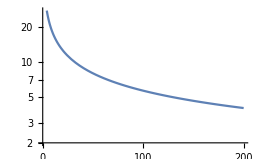

```mathematica
LogPlot[((n A h Di) Exp[h^2 Di t] Erfc[h √(Di t)])/V,{t,0,200}, PlotRange->{{0,200},{2,28}},Ticks->{{0,50,100,150,200},{2,4,6,8,10}}]
```

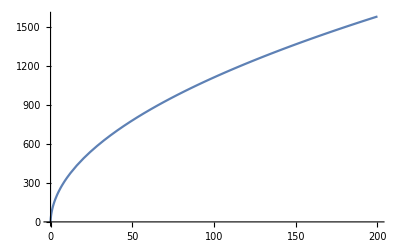

```mathematica
Plot[(n A)/(h V)(Exp[h^2 Di t] Erfc[h √(Di t)]-1+2/(√π)h √(Di t)),{t,0,200}]
```

```mathematica
plot = Plot[(n A)/(h V)(Exp[h^2 Di t] Erfc[h √(Di t)]-1+2/(√π)h √(Di t)),{t,0,200}]
```

-Graphics-

```mathematica
mydata=Flatten[Cases[plot,Line[x__]->x,Infinity],1]
```

{{4.08163×10^-6,0.00203329},{0.0613436,15.4122},{0.122683,25.3168},{0.184023,33.3493},{0.245362,40.3003},{0.306702,46.5198},{0.368041,52.201},{0.49072,62.3899},{0.55206,67.0365},{0.613399,71.4466},{0.736078,79.6819},{0.981436,94.3853},{1.04278,97.7745},{1.10412,101.069},{1.22679,107.402},{1.47215,119.206},{1.96287,140.226},{2.02421,142.663},{2.08555,145.064},{2.20823,149.764},{2.45358,158.793},{2.9443,175.605},{3.92573,205.5},{3.99223,207.384},{4.05873,209.252},{4.19173,212.943},{4.45772,220.155},{4.98972,233.966},{6.0537,259.549},{6.1202,261.07},{6.1867,262.584},{6.3197,265.587},{6.58569,271.5},{7.11769,282.98},{8.18167,304.724},{8.24376,305.949},{8.30586,307.168},{8.43004,309.594},{8.67841,314.393},{9.17515,323.789},{10.1686,341.851},{12.1556,375.508},{16.0515,434.322},{20.2777,490.518},{24.2218,537.88},{28.4962,585.037},{32.6926,628.004},{36.6069,665.661},{40.8515,704.286},{44.814,738.571},{48.6986,770.74},{52.9134,804.225},{56.8461,834.287},{61.1091,865.721},{65.2941,895.531},{69.1971,922.483},{73.4303,950.87},{77.3815,976.637},{81.6628,1003.82},{85.8662,1029.83},{89.7876,1053.53},{94.0392,1078.64},{98.0088,1101.58},{101.9,1123.63},{106.122,1147.07},{110.062,1168.53},{114.332,1191.36},{118.524,1213.36},{122.434,1233.53},{126.674,1255.05},{130.632,1274.81},{134.513,1293.89},{138.723,1314.29},{142.652,1333.05},{146.91,1353.09},{150.887,1371.55},{154.785,1389.41},{159.014,1408.53},{162.961,1426.15},{167.238,1445.},{171.437,1463.27},{175.354,1480.12},{179.601,1498.17},{183.567,1514.84},{187.454,1531.},{191.671,1548.35},{195.607,1564.36},{195.675,1564.64},{195.744,1564.92},{195.881,1565.48},{196.156,1566.59},{196.705,1568.81},{197.803,1573.23},{197.872,1573.51},{197.941,1573.79},{198.078,1574.34},{198.353,1575.44},{198.902,1577.65},{198.97,1577.93},{199.039,1578.2},{199.176,1578.75},{199.451,1579.85},{199.519,1580.13},{199.588,1580.4},{199.725,1580.96},{199.794,1581.23},{199.863,1581.51},{199.931,1581.78},{200.,1582.06}}

```mathematica
Export["/home/satya/mathematica/surface_adsorption.csv",mydata,"CSV"];
```